{{π/2,1.65532},{(7 π)/10,0.774091},{(9 π)/10,0.0791114},{(11 π)/10,0.143339},{(13 π)/10,0.913824},{(3 π)/2,1.75535}}

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{aa→1.,bb→1.,cc→1.}

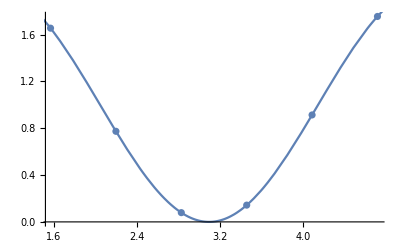

```mathematica
<<EDA`
ff=1.5;
aaa=ccc=bbb=1;
wrkpt=Table[{k,ccc+aaa Cos[ff (bbb-k)]},{k,Pi/2,3Pi/2,Pi/5}]
fit1=FindFit[wrkpt,{cc+aa Cos[ff( xx-bb)]},{aa,bb,cc},xx]
Show[{ListPlot[wrkpt],Plot[(cc/.fit1)+(aa/.fit1) Cos[ff(x-(bb/.fit1))],{x,0,2Pi}]}]
```

## Let’s add 1 counts to all and subtract 1 counts and refit the two possibilities {cc+aa Cos[ff(x-bb)]} A difference in ‘bb’ means we introduced a fake EDM

{aa→1.,bb→1.,cc→2.}

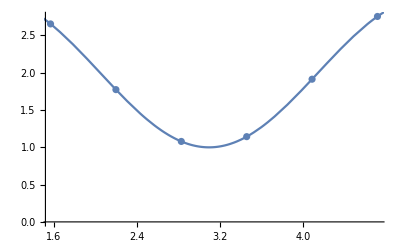

{aa→1.,bb→1.,cc→3.33067×10^-16}

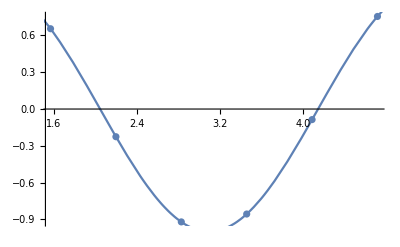

```mathematica
wrkptpos=N[MapAt[#+1&,wrkpt,{All,2}]];
fit1=FindFit[wrkptpos,{cc+aa Cos[ff(xx-bb)]},{aa,bb,cc},xx]
Show[{ListPlot[wrkptpos],Plot[(cc/.fit1)+(aa/.fit1) Cos[ff(x-(bb/.fit1))],{x,0,2Pi}]}]
wrkptneg=MapAt[#-1&,wrkpt,{All,2}];
fit1=FindFit[wrkptneg,{cc+aa Cos[ff(xx-bb)]},{aa,bb,cc},xx]
Show[{ListPlot[wrkptneg],Plot[(cc/.fit1)+(aa/.fit1) Cos[ff(x-(bb/.fit1))],{x,0,2Pi}]}]
```

## Now let’s shift all bins in one direction along x-axis by 1 step

```mathematica
wrkptrf=MapAt[#+1&,wrkpt,{All,1}];
fit1=FindFit[wrkptrf,{cc+aa Cos[ff(xx-bb)]},{aa,bb,cc},xx]
Show[{ListPlot[wrkptrf],Plot[(cc/.fit1)+(aa/.fit1) Cos[ff(x-(bb/.fit1))],{x,0,2Pi}]}];
wrkptrf2=MapAt[#-1&,wrkpt,{All,1}];
fit1=FindFit[wrkptrf2,{cc-aa Cos[ff(xx-bb)]},{aa,bb,cc},xx]
Show[{ListPlot[wrkptrf2],Plot[(cc/.fit1)-(aa/.fit1) Cos[ff(x-(bb/.fit1))],{x,0,2Pi}]}];
```

{aa→1.,bb→2.,cc→1.}

{aa→1.,bb→2.0944,cc→1.}

## Moving every bin along x-direction obviously created a different ‘bb’ and this mimics an EDM. This is most likely what is done in Blinding.